## Import Utils

```mathematica
Get["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

```mathematica
(*NotebookEvaluate["D:\\Documents\\workspace\\课题\\PN_inverse\\InversePNUtils.nb"]*)
```

```mathematica
NotebookEvaluate["D:\\Documents\\workspace\\课题\\workspace\\Local\\Public\\mathematica\\PN_inverse\\InversePNUtils.nb"];
```

输入Mc范围：{8,15}

输入q范围：{1,20}

m1范围：{9.18959,91.4002}

m2范围：{2.43734,17.2305}

输入Mc范围：{6,13}

输入q范围：{1,7}

m1范围：{6.89219,42.9142}

m2范围：{2.8295,14.9331}

全局极小值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极大值结果：{0.,{m1→3.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{2.81559×10^-11,{m1→46.8969,m2→60.4341,spin1z→0.435746,spin2z→-0.638885}}

全局极大值结果：{8.65708,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

全局极小值结果：{8.47209×10^-10,{m1→60.1419,m2→76.87,spin1z→0.320417,spin2z→-0.443897}}

全局极大值结果：{1.94773,{m1→100.,m2→3.,spin1z→0.99,spin2z→0.99}}

### Read from CSV

```mathematica
baseDir="D:\\Documents\\workspace\\课题\\workspace\\Local\\Parameterized_PN_Tests\\csv";
eventID="GW250114";

(*键名直接用短名，里面加上下划线*)
inspiralParams={"dphi_2","dphi_3","dphi_4","dphi_5l","dphi_6","dphi_7"};
intermediateParams={};
mergerParams={};

allParams=Join[inspiralParams,intermediateParams,mergerParams];

(* ==================读取函数==================*)
readDeviationFile[shortName_]:=Module[{path,raw},(*短名拼接上 _IMRP_posterior 还原成完整文件名*)path=FileNameJoin[{baseDir,eventID,shortName<>"_IMRP_posterior.csv"}];
raw=Import[path];
(*提取前五列*){raw[[2;;,1]],(*m1*)raw[[2;;,2]],(*m2*)raw[[2;;,3]],(*spin1z*)raw[[2;;,4]],(*spin2z*)raw[[2;;,5]]  (*偏差参数值*)}]

(*批量读取，键名就是传入的 shortName*)
readAllDeviations[]:=AssociationMap[readDeviationFile,allParams]

(* ==================执行==================*)
samples=readAllDeviations[];
```

## Calculate GR pars and further Transform $\delta$ into parameterized pars

```mathematica
(*批量计算非自旋 GR 系数值*)getGRValues[paramName_,m1s_,m2s_,chi1L_,chi2L_]:=Module[{etas},etas=etaFromMasses[m1s,m2s];
Switch[paramName,(*(* =====Alpha (并合段)=====*)"dalpha_3",IMRPhenomDAlphaNS[3,m1s,m2s,0,0],"dalpha_4",IMRPhenomDAlphaNS[4,m1s,m2s,0,0],"dalpha_2",IMRPhenomDAlphaNS[2,m1s,m2s,0,0],(* =====Beta (过渡段)=====*)"dbeta_2",IMRPhenomDBetaNS[2,m1s,m2s,0,0],"dbeta_3",IMRPhenomDBetaNS[3,m1s,m2s,0,0],*)(* =====Phi (旋近段)=====因为设置了 Listable，直接把整个 m1s,m2s 列表传进去即可，内部会自动对每个元素计算并返回列表*)"dphi_0",IMRPhenomXASPhiNS[0,m1s,m2s,chi1L,chi2L],
"dphi_2",IMRPhenomXASPhiNS[2,m1s,m2s,chi1L,chi2L],
"dphi_3",IMRPhenomXASPhiNS[3,m1s,m2s,chi1L,chi2L],
"dphi_4",IMRPhenomXASPhiNS[4,m1s,m2s,chi1L,chi2L],
"dphi_5l",IMRPhenomXASPhiLNS[5,m1s,m2s,chi1L,chi2L],
"dphi_6",IMRPhenomXASPhiNS[6,m1s,m2s,chi1L,chi2L],
"dphi_6l",IMRPhenomXASPhiLNS[6,m1s,m2s,chi1L,chi2L],
"dphi_7",IMRPhenomXASPhiNS[7,m1s,m2s,chi1L,chi2L],
_,ConstantArray[0,Length[m1s]]]];


(* ==========对所有参数追加第6列(GR值)和第7列(参数化值)==========*)
Do[Module[{grVals,paramVals},(*第6列：非自旋 GR 系数值*)grVals=getGRValues[p,samples[p][[1]],samples[p][[2]],samples[p][[3]],samples[p][[4]]];
(*第7列：参数化值=GR×(1+d)*)paramVals=grVals*(1+samples[p][[5]]);
(*拼接到原来的5列后面*)samples[p]=Join[samples[p],{grVals,paramVals}];],{p,allParams}];
```

```mathematica
|p-50|*2
```

## m1-m2 Plot, 22

```mathematica
plots=<||>;
compPlots=<||>;
```

## INSPIRAL

### phi_2

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_2"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,45},{1,1.5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.20528};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p],PlotPoints->150,MaxRecursion->4];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]],1.5},"",False][[1]][[2]];
(*prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],contourPoints[p],"",False][[1]][[2]];*)

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,45}

输入q范围：{1,1.5}

m1范围：{28.7175,63.5678}

m2范围：{23.5436,51.6914}

对称数据：原始 147606 + 镜像 147606

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 0.99999（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

对称边界框：{23.5436, 63.5678} × {23.5436, 63.5678}

等高线值：{0.20528}，共 2 条

第一条前3点：{{32.6002,32.4755},{32.6012,32.4734},{32.6075,32.4583}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

警告：第 2 个区域点数不足，跳过积分

=====  =====

包含片段数：2 (合并模式: False)

区域内总积分值：0.16

可信水平百分比：16.%

==========================

dphi_2 预处理完成，红线包含概率 prob = 0.16

```mathematica
m1m2PDF[p][34,34]
```

0.00422641

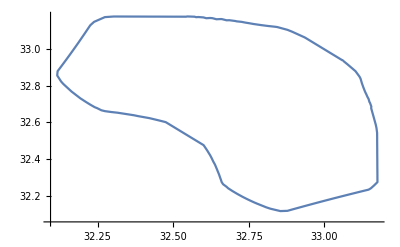

```mathematica
ListLinePlot[mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]]
```

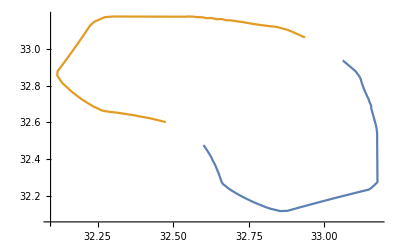

```mathematica
ListLinePlot[contourPoints[p]]
```

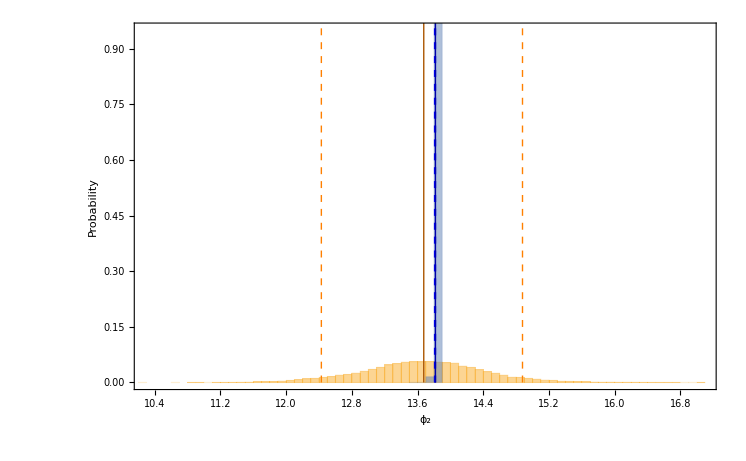

```mathematica
p="dphi_2"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["2",Italic]
,50
,Automatic
]
```

====== [dphi_2] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.42, 0.58}

实际使用的 GR 概率区间上下界: {13.8167, 13.8173}

实际使用的 Param 概率区间上下界: {13.5303, 13.8172}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=8.59757×10^-16

GR上界: 点数=250 | Y>0点数=250 | 平均误差=8.95284×10^-16

Param下界: 点数=250 | Y>0点数=250 | 平均误差=5.54223×10^-16

Param上界: 点数=250 | Y>0点数=250 | 平均误差=8.45546×10^-16

{{31.51,58.0325},{31.52,58.051},{31.53,58.0694},{31.54,58.0878},{31.55,58.1062}}

{{31.51,32.4022},{31.52,32.4125},{31.53,32.4228},{31.54,32.433},{31.55,32.4433}}

chi1L取值：-0.0486105

chi2L取值：-0.0272827

=====================================================

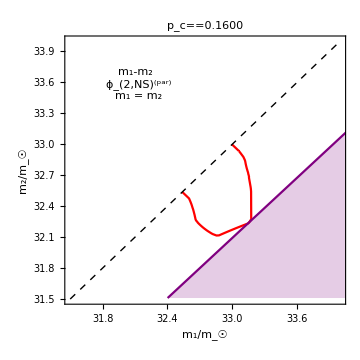

```mathematica
probability=prob;
(*probability=0.16;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhi,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1,2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_4

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_4"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.173155};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p],PlotPoints->150,MaxRecursion->4];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]],2]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 145184 + 镜像 145184

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.173155}，共 2 条

第一条前3点：{{32.6651,32.5496},{32.6763,32.5416},{32.6923,32.5371}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.130261

可信水平百分比：13.0261%

==========================

dphi_4 预处理完成，红线包含概率 prob = 0.130261

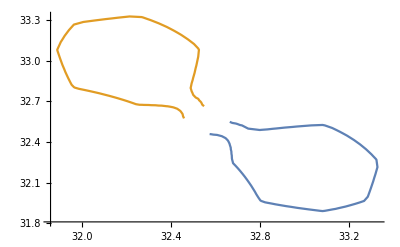

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

```mathematica
m1m2PDF[p][33,32.5]
```

0.17571

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.43487, 0.56513}

实际使用的 GR 概率区间上下界: {212.727, 212.754}

实际使用的 Param 概率区间上下界: {190.156, 212.75}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=2.30784×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=1.42109×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=1.73941×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=1.4893×10^-14

{{31.51,100.157},{31.52,100.189},{31.53,100.221},{31.54,100.252},{31.55,100.284}}

{{31.51,32.7828},{31.52,32.7932},{31.53,32.8036},{31.54,32.814},{31.55,32.8244}}

chi1L取值：-0.0439774

chi2L取值：-0.0295357

=====================================================

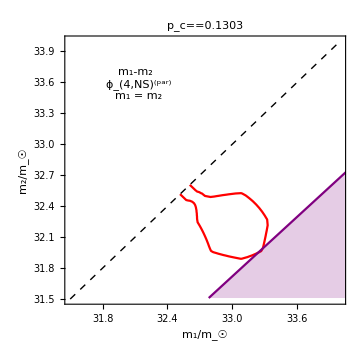

```mathematica
probability=prob;
(*probability=0.13;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

```mathematica
probability=prob;
(*probability=0.13;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiNS,spinPercentile1->0.15,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

====== [dphi_4] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.43487, 0.56513}

实际使用的 GR 概率区间上下界: {212.727, 212.754}

实际使用的 Param 概率区间上下界: {190.156, 212.75}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=2.30784×10^-14

GR上界: 点数=250 | Y>0点数=250 | 平均误差=1.42109×10^-14

Param下界: 点数=250 | Y>0点数=250 | 平均误差=1.73941×10^-14

Param上界: 点数=250 | Y>0点数=250 | 平均误差=1.4893×10^-14

{{31.51,100.157},{31.52,100.189},{31.53,100.221},{31.54,100.252},{31.55,100.284}}

{{31.51,32.7828},{31.52,32.7932},{31.53,32.8036},{31.54,32.814},{31.55,32.8244}}

chi1L取值：-0.232911

chi2L取值：-0.0295357

=====================================================

-Graphics-

### phi_5l

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_5l"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.18068383};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 143483 + 镜像 143483

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.180684}，共 2 条

第一条前3点：{{32.6448,32.7604},{32.6386,32.7689},{32.6165,32.7986}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.0953348

可信水平百分比：9.53348%

==========================

dphi_5l 预处理完成，红线包含概率 prob = 0.0953348

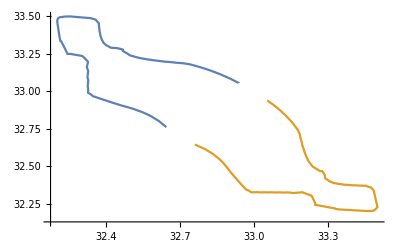

```mathematica
ListLinePlot[contourPoints[p]]
```

```mathematica
p="dphi_5l";
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.45235, 0.54765}

实际使用的 GR 概率区间上下界: {1043.98, 1043.98}

实际使用的 Param 概率区间上下界: {1043.98, 1067.19}

GR下界: 点数=450 | Y>0点数=450 | 平均误差=4.19378×10^-13

GR上界: 点数=450 | Y>0点数=450 | 平均误差=2.59206×10^-13

Param下界: 点数=450 | Y>0点数=450 | 平均误差=1.60172×10^-13

Param上界: 点数=450 | Y>0点数=450 | 平均误差=3.31966×10^-13

{{30.51,31.801},{30.52,31.8114},{30.53,31.8218},{30.54,31.8323},{30.55,31.8427}}

{{30.51,246.133},{30.52,246.214},{30.53,246.295},{30.54,246.375},{30.55,246.456}}

chi1L取值：-0.019432

chi2L取值：-0.0232529

=====================================================

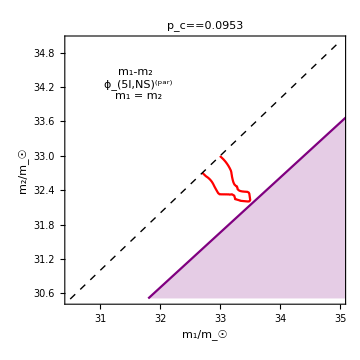

```mathematica
probability=prob;
probability=0.0953;
plots[p]=PlotInversion[p,probability,30.5,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiLNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

0.175

====== [dphi_5l] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.4125, 0.5875}

实际使用的 GR 概率区间上下界: {1043.98, 1043.99}

实际使用的 Param 概率区间上下界: {1034.04, 1077.48}

GR下界: 点数=450 | Y>0点数=450 | 平均误差=45.5247

GR上界: 点数=450 | Y>0点数=450 | 平均误差=45.5155

Param下界: 点数=450 | Y>0点数=450 | 平均误差=55.4573

Param上界: 点数=450 | Y>0点数=450 | 平均误差=12.0198

{{30.51,30.51},{30.52,30.52},{30.53,30.53},{30.54,30.54},{30.55,30.55}}

{{30.51,30.51},{30.52,30.52},{30.53,30.53},{30.54,30.54},{30.55,30.55}}

chi1L取值：-0.0316921

chi2L取值：-0.0232529

=====================================================

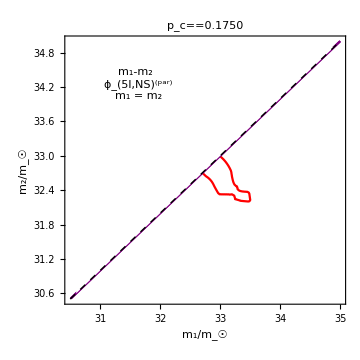

```mathematica
probability=0.175
plots[p]=PlotInversion[p,probability,30.5,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiL,spinPercentile1->0.45,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_6

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_6"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,2}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
contourPD[p]={0.13458};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",False][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,2}

m1范围：{28.7175,57.5313}

m2范围：{20.5469,40.2044}

对称数据：原始 135767 + 镜像 135767

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{20.5469, 57.5313} × {20.5469, 57.5313}

等高线值：{0.13458}，共 2 条

第一条前3点：{{32.3667,32.4822},{32.3386,32.5027},{32.3135,32.5234}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: False)

区域内总积分值：0.339732

可信水平百分比：33.9732%

==========================

dphi_6 预处理完成，红线包含概率 prob = 0.339732

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_6] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.330134, 0.669866}

实际使用的 GR 概率区间上下界: {-12123.9, -12118.1}

实际使用的 Param 概率区间上下界: {-12118.3, -10647.6}

GR下界: 点数=250 | Y>0点数=250 | 平均误差=2.67028×10^-12

GR上界: 点数=250 | Y>0点数=250 | 平均误差=2.37196×10^-12

Param下界: 点数=250 | Y>0点数=250 | 平均误差=3.17232×10^-12

Param上界: 点数=250 | Y>0点数=250 | 平均误差=2.02999×10^-12

{{31.51,33.4192},{31.52,33.4298},{31.53,33.4404},{31.54,33.451},{31.55,33.4616}}

{{31.51,78.2379},{31.52,78.2627},{31.53,78.2875},{31.54,78.3124},{31.55,78.3372}}

chi1L取值：-0.032519

chi2L取值：-0.0183631

=====================================================

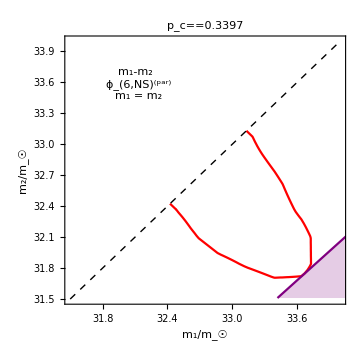

```mathematica
probability=prob;
(*probability=0.34;*)

plots[p]=PlotInversion[p,probability,31.5,34,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{1},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

### phi_7

```mathematica
(* ==========================================*)(*阶段一：预处理（算概率、提取红线）*)(* ==========================================*)
p="dphi_7"; (*换参数改这里*)

m1Data=samples[p][[1]];
m2Data=samples[p][[2]];

(*算 PDF*)
m1m2[p]=Transpose[{m1Data,m2Data}];
{m1PriorRange[p],m2PriorRange[p]}=ChirpQRangeToMassRange[{25,35},{1,1.5}];
m1m2PDF[p]=GetNormalizedPDF[m1m2[p],m1PriorRange[p],m2PriorRange[p]];

(*提取 0.005 密度对应的红线*)
(*q<=2*)
(*contourPD[p]={0.16305384};*)
(*contourPD[p]={0.1629871};*)
contourPD[p]={0.162987};
{contourPlotObj[p],contourPoints[p]}=GetContourPlotAndPoints[m1m2PDF[p],m1PriorRange[p],m2PriorRange[p],contourPD[p]];
contourPoints[p][[1]]=SmoothContour[contourPoints[p][[1]]];

(*算出红线内部包含的真实后验概率 prob*)
prob=CalculateCredibleLevelsFromContours[m1m2PDF[p],{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]},"",True][[1]][[2]];

Print[p," 预处理完成，红线包含概率 prob = ",prob];
```

输入Mc范围：{25,35}

输入q范围：{1,1.5}

m1范围：{28.7175,49.4416}

m2范围：{23.5436,40.2044}

对称数据：原始 143218 + 镜像 143218

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

对称先验空间积分 = 1.（应接近1）

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

归一化验证 = 1.

Set::wrsym: Symbol Automatic is Protected.

对称边界框：{23.5436, 49.4416} × {23.5436, 49.4416}

等高线值：{0.162987}，共 2 条

第一条前3点：{{32.6186,32.6966},{32.6132,32.6992},{32.6047,32.7031}}

Set::setps: contourPoints[p] in the part assignment is not a symbol.

[合并模式] 将 1 个片段强制合并为一个多边形进行积分...

NIntegrate::regm: Method LocalAdaptive is not applicable for a region domain. Continuing with method Automatic.

=====  =====

包含片段数：1 (合并模式: True)

区域内总积分值：0.254659

可信水平百分比：25.4659%

==========================

dphi_7 预处理完成，红线包含概率 prob = 0.254659

```mathematica
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],(*第6列：GR理论预测样本*)Range[10,100,1],(*m1 范围*)orderVal,(*阶数 order*)Median[chi1Data],(*自旋1*)Median[chi2Data]           (*自旋2*)]
```

====== [dphi_7] 反解校验报告 (容差: 1/100000) ======

实际使用的概率区间上下界: {0.40375, 0.59625}

实际使用的 GR 概率区间上下界: {16345.9, 16346.5}

实际使用的 Param 概率区间上下界: {16347., 19481.}

GR下界: 点数=400 | Y>0点数=400 | 平均误差=3.63798×10^-12

GR上界: 点数=400 | Y>0点数=400 | 平均误差=3.7744×10^-13

Param下界: 点数=400 | Y>0点数=400 | 平均误差=1.83263×10^-12

Param上界: 点数=400 | Y>0点数=400 | 平均误差=3133.96

{{31.01,31.2717},{31.02,31.2817},{31.03,31.2918},{31.04,31.3019},{31.05,31.312}}

{{31.01,31.0108},{31.02,31.0198},{31.03,31.0306},{31.04,31.0396},{31.05,31.0508}}

chi1L取值：-0.0325528

chi2L取值：-0.0219549

=====================================================

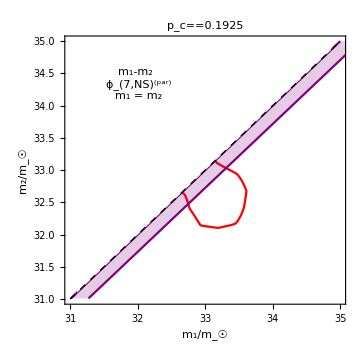

```mathematica
probability=prob;
probability=0.1925;
(*0.32*)
plots[p]=PlotInversion[p,probability,31,35,0.01,cm->True,cd->True,cu->True,plotgr->False,projX->False,projY->False,funcName->IMRPhenomXASPhiNS,spinPercentile1->0.5,spinPercentile2->0.5,contourIndices->{2},m1m2region->{mergeSymmetricCurves[contourPoints[p][[1]],contourPoints[p][[2]]]}]
```

```mathematica
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\",eventID}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,".pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>".pdf"}],plots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[plots]}]
```

正在导出矢量图: plot_dphi_5l.pdf ...

# 123

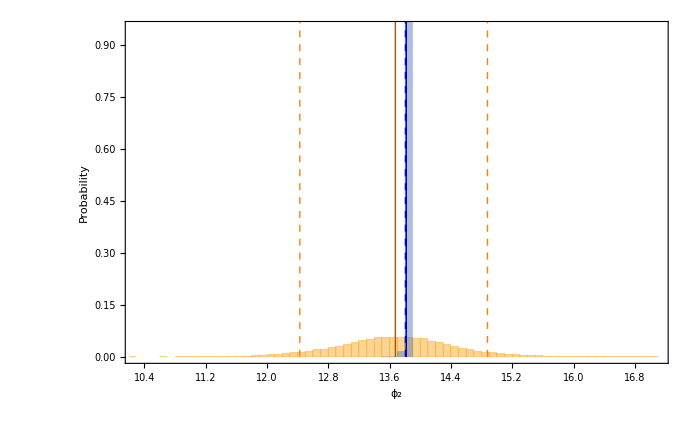

正在导出矢量图: plot_dphi_2_comp.pdf ...

正在导出矢量图: plot_dphi_5l_comp.pdf ...

```mathematica
p="dphi_2"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["2",Italic]
,50
,Automatic
]
p="dphi_5l"; 
compPlots[p]=PlotComparisonBetween[samples[p][[7]],(*第7列：参数化系数样本*)samples[p][[6]],Style["5l",Italic]
,50
,Automatic
];
(*1. 定义你要存放 PDF 的文件夹名称*)
targetDir=FileNameJoin[{"D:\\Documents\\workspace\\课题\\论文\\fig\\","comp"}];

(*2. 如果目录不存在，则自动创建*)
If[!DirectoryQ[targetDir],CreateDirectory[targetDir];
Print["已自动创建目录: ",targetDir]];

Do[Print["正在导出矢量图: plot_",key,"_comp.pdf ..."];
Export[FileNameJoin[{targetDir,eventID<>"_"<>key<>"_comp.pdf"}],compPlots[key],"PDF",AllowRasterization->False (*强制全矢量输出，绝对高清*),ImageSize->500],
{key,Keys[compPlots]}]
```